# GeneralizedVoronoiMesh

Computes Voronoi mesh for groups of points, useful for approximating Voronoi diagram for arbitrary geometries.

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
(* Input validation *)
isListOfPoints[_]:=False;
isListOfPoints[list_List]:=AllTrue[list,Length[#]==2&&AllTrue[#, NumericQ]&];

isGeneralizedInput[_]:=False;
isGeneralizedInput[curves_List]:=Length[curves]>1&&AllTrue[curves,isListOfPoints];

(* Function to combine Voronoi cells, this is the most expensive part of the algorithm
  because of the very complex pattern matching logic. There's probably some Mathematica
  function which does this but I haven't been able to find anything *)
combinePolygons[listOfPolygons_]:=listOfPolygons//.{
(* Merge polygons sharing an edge, multiple cases to handle polygon rotations *)
{a___,Polygon[{d___,x_,y_,e___}],b___,Polygon[{f___,y_,x_,g___}],c___}->{a,b,c,Polygon[{d,x,g,f,y,e}]},
{a___,Polygon[{d___,x_,y_,e___}],b___,Polygon[{x_,f___,y_}],c___}->{a,b,c,Polygon[{d,x,f,y,e}]},
{a___,Polygon[{y_,d___,x_}],b___,Polygon[{f___,y_,x_,g___}],c___}->{a,b,c,Polygon[{f,y,d,x,g}]},
{a___,Polygon[{y_,d___,x_}],b___,Polygon[{x_,f___,y_}],c___}->{a,b,c,Polygon[{x,f,y,d}]},
(* Simplify polygons that contain overlapping edges, such cases might arise due to merge transformations *)
Polygon[{a___,x_,y_,x_,b___}]->Polygon[{a,x,b}],
Polygon[{y_,x_,a___,x_}]->Polygon[{x,a}],
Polygon[{x_,a___,x_,y_}]->Polygon[{x,a}]};

GeneralizedVoronoiMesh[curves_?isGeneralizedInput,bounds_:Nothing,opts:OptionsPattern[]]:=Module[
{seeds,mesh,permutation,sortedCells,groupedCells,newPolygons},
(* Get seed points from curves and generate a Voronoi mesh *)
seeds=Join@@curves;
mesh=VoronoiMesh[seeds,bounds];

(* Get a permutation of mesh cells so that cell_i corresponds to seed_i *)
(* Source: https://mathematica.stackexchange.com/a/109687/30248 *)
permutation=Last/@Region`Mesh`MeshMemberCellIndex[mesh][seeds]; 

(* "unflatten" - collect polygons for each seed group *)
sortedCells=MeshCells[mesh,2][[permutation]];
groupedCells=TakeList[sortedCells,Length/@curves];

(* Combine all polygons in a group into one polygon *)
newPolygons=combinePolygons/@groupedCells;

(* Create a mesh out of the polygons *)
MeshRegion[MeshCoordinates[mesh],Flatten[newPolygons],opts]];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

GeneralizedVoronoiMesh[{g_1,g_2,…}]

gives the MeshRegion that represents the Voronoi mesh for lists of 2D points g_1,g_2, ….

GeneralizedVoronoiMesh[{g_1,g_2,…},{{x_min,x_max},{y_min,y_max}}]

clips the mesh to the bounds [x_min, x_max] × [y_min, y_max].

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

GeneralizedVoronoiMesh takes the same options as MeshRegion.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Generate the Voronoi mesh for a some points, lines and a parabola:

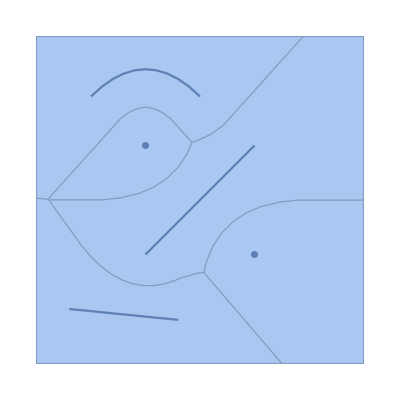

```mathematica
With[
{parabola=Table[{t,1.7-t*t},{t,-0.5,0.5,0.1}],
line1=Table[{t,t},{t,0,1,0.1}],
line2=Table[{t-0.7,-0.5-0.1t},{t,0,1,0.1}],
point1={1,0},point2={0,1}},
Show[
GeneralizedVoronoiMesh[
{parabola,line1,line2,{point1},{point2}},
{{-1,2},{-1,2}}],
ListLinePlot/@{parabola,line1,line2},
ListPlot[{point1,point2}]]]
```

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

Since MeshRegion cannot contain polygons with holes, the Voronoi meshes which contain such polygons will contain edges so that such polygons can be represented without holes:

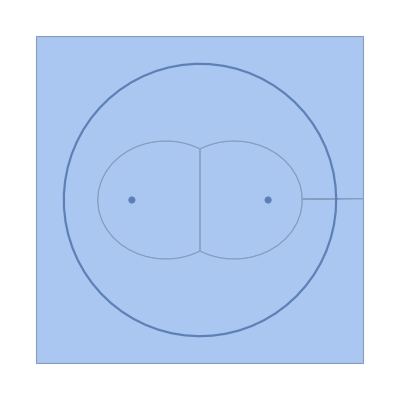

```mathematica
With[
{circle=Table[AngleVector[t],{t,0,2Pi+0.1,0.1}],
point1={-0.5,0},point2={0.5,0}},
Show[
GeneralizedVoronoiMesh[
{circle,{point1},{point2}},
{{-1.2,1.2},{-1.2,1.2}}],
ListLinePlot[circle],
ListPlot[{point1,point2}]]]
```

### Neat Examples

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Lakshay Garg

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

keyword 1

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

VoronoiMesh

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

Resource Name (resources from any Wolfram repository)

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Source, reference or citation information

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

Link to other related material

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

If one is not interested in a MeshRegion but only the polygons, here’s an alternative approach which handles polygons with holes gracefully

```mathematica
(*
GeneralizedVoronoiCells[curves_] := Module[
{seeds, mesh, permutation, sortedCells, groupedCells},
seeds = Join@@curves;
mesh = VoronoiMesh[seeds];
permutation = Last/@Region`Mesh`MeshMemberCellIndex[mesh][seeds];
sortedCells = MeshCells[mesh, 2][[permutation]];
groupedCells = TakeList[sortedCells, Length /@ curves];
CanonicalizePolygon /@ Graphics`PolygonUtils`PolygonCombine /@ groupedCells];
*)
```

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.